```mathematica
(* 
Terahertz wave propagation in uniform nanorods:A nonlocal continuum
mechanics formulation including the effect of lateral inertia
S.Narendar
 *)
```

```mathematica
Clear[Evaluate[Context[]<>"*"]];
Needs["PlotLegends`"]

u[x_,t_]:= Exp[-I(k x - ω t)]
ωCl[k_]=Solve[D[u[x,t],{x,2}]==(ρ/Ev)D[u[x,t],{t,2}],ω][[2,1,2]];
ωStrainG[k_]=Solve[α^2 D[u[x,t],{x,4}]+D[u[x,t],{x,2}]==(ρ/Ev)D[u[x,t],{t,2}],ω][[2,1,2]]//FullSimplify;
ωStrain4G[k_]=Solve[ α^4 D[u[x,t],{x,6}]+ α^2 D[u[x,t],{x,4}]+D[u[x,t],{x,2}]==(ρ/Ev)D[u[x,t],{t,2}],ω][[2,1,2]]//FullSimplify;
ωStressG[k_]= Solve[D[u[x,t],{x,2}]+(ρ/Ev)α^2 D[D[u[x,t],{t,2}],{x,2}]==(ρ/Ev)D[u[x,t],{t,2}],ω][[2,1,2]];
ωBK[k_]=(2/0.142)Sqrt[Ev/ρ]Sin[k * 0.142/2];
ωStressGIn[k_]=Solve[Ev D[u[x,t],{x,2}]== ρ D[u[x,t],{t,2}] - ρ ν^2ζ^2 D[D[u[x,t],{t,2}],{x,2}]-α^2 ρ D[D[u[x,t],{t,2}],{x,2}]+α^2 ρ ν^2ζ^2D[D[u[x,t],{t,2}],{x,4}],ω][[2,1,2]]
```

(√Ev k)/(√(1+k^2 α^2+k^2 ζ^2 ν^2+k^4 α^2 ζ^2 ν^2) √ρ)

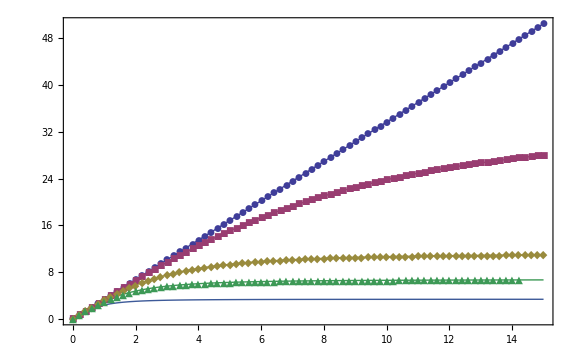

```mathematica
Block [{Ev = 1.03 * 10^12,
ρ = 2300,
(*α= 0.1 ,*)
r = 3.5 * 10^(-9),
t = 0.35 * 10^(-9),
A = 2 * Pi * r * t,
a=0.142,
ν = 0.280, (* Poisson's ratio *)
L=0.238 10^(-9)
},
ζ = Sqrt[(r^2)/2+(L^2)/12]; (* Radius of gyration of a cylindrical rod *)


points1=Block[{α=0},Table[{x,ωStressGIn[x]/(2000 Pi)},{x,Range[0,15,0.2]}]];
points2=Block[{α=0.1},Table[{x,ωStressGIn[x]/(2000 Pi)},{x,Range[0,15,0.2]}]];
points3=Block[{α=0.3},Table[{x,ωStressGIn[x]/(2000 Pi)},{x,Range[0,15,0.2]}]];
points4=Block[{α=0.5},Table[{x,ωStressGIn[x]/(2000 Pi)},{x,Range[0,15,0.2]}]];
points5=Block[{α=1},Table[{x,ωStressGIn[x]/(2000 Pi)},{x,Range[0,15,0.2]}]];

ListLinePlot[{points1,points2,points3,points4,points5},PlotMarkers->Automatic,
PlotRange->Full,
PlotLegend->{"Local Model","e0a = 0 nm",
"e0a = 0.1 nm",
"e0a = 0.3 nm","e0a = 0.5 nm","e0a = 1.0 nm"
},
LegendShadow->None,
LegendPosition->{-0.8,0},
LegendSize->{0.5,0.5},
ImageSize->Large,
FrameLabel->{"Wave number (1/nm)","Frequency (THz)"},
Frame->True
]
]
```

```mathematica
Flatten[{(ωCl[k]/(1000 4 Pi))/.{k->Range[0,15]},Range[0,15]},{{2},{1}}]
```